```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["NDSolve`FEM`"];
```

```mathematica
Names["DifferentialEquations`NDSolveProblems`Private`*"];
(*turn off mathematica messages 
*)
$Messages={};
(*turn on mathematica messages
$Messages=$Output;
*)
```

```mathematica
(*
upper limit of integration is xinf in [nm] 
*)

xinf=100;


(*constants and parameters to use*)

kBTeV=10^-3*25.8518;
kBTkjmol=2.4943;
kj2ev=0.01036427;
mol2invnmcube=0.6022;

rho1M=mol2invnmcube;


(*
slip lengths in nm
*)
bGra=19.6;
bBN=4.0;


(* mass of water molecule in grams*)
NA=6.022*10^23;
Mwat=18/NA;
(* conversion from cm^-3 to nm^-3*)
invcm3toinvnm3=(10^7)^3;
(*conversion of mass density in g/cm^-3 to number density of water in nm^-3*)
gramspercm3toinvnm3=1.0/(Mwat*invcm3toinvnm3);

(*
epsilon zero in e/(nm*V)
*)
eps0=0.055;
epsr=78.0;
eps=eps0*epsr;


(*bjerrum length*)
lB= 1./(kBTeV*eps*4.0*Pi);

qcat=1.;
qan=-1.;

(*
concentration in molar and debye length in nanometers
*)
ConcFracValues=Sort[Flatten[Table[PowerRange[i*0.0001,i*1.0],{i,1,9}]]][[;;-4]];
DebyeLenValues=3.04/10.0/Sqrt[ConcFracValues];
```

```mathematica
(*
use a step polarization model for the dielectric constant
*)

x0=0.0;
Epsfunc[x_,x0_]:=((epsr-1)*HeavisideTheta[x-x0] + 1)*eps0;
```

## Set x0 = 0 ( in nm) in order to calculate the transport integrals and solve the mPB equation by using a model of the dielectric constant equal to the bulk water dielectric constant throughout the system. Set x0 = 0.35 in order to use a step polarization model where the dielectric constant profile is modelled as a step function and x0 is the height at which the dielectric constant changes from being equal to the vacuum to the bulk water dielectric constant

```mathematica
DDIR=NotebookDirectory[];
FDIR=DDIR<>"data_preprocessed/";
Which[x0==0.0,
EXPDIR=DDIR<>"mPB_integrals/",x0==0.33,EXPDIR=DDIR<>"mPB_integrals_eps/"];
```

## Import free energies and water density profile and export them by extending to a 100 nm-thick water film assuming that bulk water is obtained after 1.5 nm Additionally the bulk reference value for the free energy (and for the water density profiles) are obtained by averaging the free energy (and the water density profile) profile in a range between 1.0 and 1.5 nm.

```mathematica
MeanRhoWatGra=Import[FDIR<>"WatGraIntegratedDens.dat","Table"][[All,All]];
MeanRhoWatBN=Import[FDIR<>"WatBNIntegratedDens.dat","Table"][[All,All]];

heightWat=MeanRhoWatGra[[All,1]];
dzwat=heightWat[[2]]-heightWat[[1]];

BulkWatDens=(Mean[Select[MeanRhoWatGra ,(1.0<#[[1]]<1.5)&][[All,2]]] + Mean[Select[MeanRhoWatBN,(1.0<#[[1]]<1.5)&][[All,2]]] )*0.5;

lastwat=Table[{ MeanRhoWatGra[[-175,1]]+ dzwat*i,BulkWatDens},{i,1,2500,1}];
MeanRhoWatGraLim=Join[MeanRhoWatGra[[;;-175]],lastwat];
lastwat=Table[{ MeanRhoWatBN[[-175,1]]+ dzwat*i,BulkWatDens},{i,1,2500,1}];
MeanRhoWatBNLim=Join[MeanRhoWatBN[[;;-175]],lastwat];
```

```mathematica
FreeEnergyGraI = Import[FDIR<>"FreeEnergyGraI.dat","Table"][[2;;,All]];
FreeEnergyGraK=Import[FDIR<>"FreeEnergyGraK.dat","Table"][[2;;,All]];
FreeEnergyBNK=Import[FDIR<>"FreeEnergyBNK.dat","Table"][[2;;,All]];
FreeEnergyBNI=Import[FDIR<>"FreeEnergyBNI.dat","Table"][[2;;,All]];


idxes=Flatten[Position[FreeEnergyGraI[[All,1]],_?(#>1 && #<1.5&) ]];
meanFreeEn=Mean[FreeEnergyGraI[[idxes,2]]];
FreeEnergyGraI = FreeEnergyGraI[[All,{1,2}]]/.{x_,y_}->{x,kj2ev( y-meanFreeEn)};

idxes=Flatten[Position[FreeEnergyGraK[[All,1]],_?(#>1 && #<1.5&) ]];
meanFreeEn=Mean[FreeEnergyGraK[[idxes,2]]];
FreeEnergyGraK = FreeEnergyGraK[[All,{1,2}]]/.{x_,y_}->{x,kj2ev( y-meanFreeEn)};

idxes=Flatten[Position[FreeEnergyBNI[[All,1]],_?(#>1 && #<1.5&) ]];
meanFreeEn=Mean[FreeEnergyBNI[[idxes,2]]];
FreeEnergyBNI = FreeEnergyBNI[[All,{1,2}]]/.{x_,y_}->{x,kj2ev( y-meanFreeEn)};

idxes=Flatten[Position[FreeEnergyBNK[[All,1]],_?(#>1&& #<1.5&) ]];
meanFreeEn=Mean[FreeEnergyBNK[[idxes,2]]];
FreeEnergyBNK = FreeEnergyBNK[[All,{1,2}]]/.{x_,y_}->{x,kj2ev( y-meanFreeEn)};


dzBNK=FreeEnergyBNK[[2,1]]-FreeEnergyBNK[[1,1]];
dzGRAK=FreeEnergyGraK[[2,1]]-FreeEnergyGraK[[1,1]];
dzGRAI=FreeEnergyGraI[[2,1]]-FreeEnergyGraI[[1,1]];
dzBNI=FreeEnergyBNI[[2,1]]-FreeEnergyBNI[[1,1]];

idxes=Flatten[Position[FreeEnergyGraK[[All,1]],_?( #<1.5&) ]];

lastGK=Table[{FreeEnergyGraK[[-1,1]]+ dzGRAK*i,0.0},{i,1,100000,1}];
FreeEnergyGraK=Join[FreeEnergyGraK[[idxes,All]],lastGK];

idxes=Flatten[Position[FreeEnergyGraI[[All,1]],_?( #<1.5&) ]];
lastGI=Table[{FreeEnergyGraI[[-1,1]]+ dzGRAI*i,0.0},{i,1,100000,1}];
FreeEnergyGraI=Join[FreeEnergyGraI[[idxes,All]],lastGI];

idxes=Flatten[Position[FreeEnergyBNK[[All,1]],_?( #<1.5&) ]];
lastBK=Table[{FreeEnergyBNK[[-1,1]]+ dzBNK*i,0.0},{i,1,100000,1}];
FreeEnergyBNK=Join[FreeEnergyBNK[[idxes,All]],lastBK];

idxes=Flatten[Position[FreeEnergyBNI[[All,1]],_?( #<1.5&) ]];
lastBI=Table[{FreeEnergyBNI[[-1,1]]+ dzBNI*i,0.0},{i,1,100000,1}];
FreeEnergyBNI=Join[FreeEnergyBNI[[idxes,All]],lastBI];
```

```mathematica
FGRAI=Interpolation[FreeEnergyGraI,InterpolationOrder->1];

FGRAK=Interpolation[FreeEnergyGraK,InterpolationOrder->1];

FBNK=Interpolation[FreeEnergyBNK,InterpolationOrder->1];

FBNI=Interpolation[FreeEnergyBNI,InterpolationOrder->1];

Export[EXPDIR<>"FreeEnergy_gra_bn_ik.dat",Table[{x,FGRAI[x],FGRAK[x],FBNI[x],FBNK[x]},{x,0,xinf,0.01}]];
```

```mathematica
(* function to solve poisson-boltzmann equation numerically with a grid element of 0.01 nm *)

solvePsi=Compile[{{xinf, _Real},{sigma,_Real},{rhofrac,_Real},{DeltaGI,_Real,1},{DeltaGK,_Real,1}},NDSolve[{Inactivate[  Div[Epsfunc[x,x0]Grad[  y[x],{x}],{x}],Div|Grad]  +qan rho1M rhofrac Exp[-( DeltaGI[x] + qan  y[x])/kBTeV ] + qcat   rho1M rhofrac Exp[-( DeltaGK[x]+ qcat  y[x])/kBTeV ] ==0.0 +  NeumannValue[-sigma/eps,x==0] ,y[xinf]==0},y,x∈ToElementMesh[ImplicitRegion[0≤x≤xinf,x],MaxCellMeasure->0.01],Method->"FiniteElement" ],
RuntimeAttributes->{Listable},Parallelization->True,CompilationTarget->"C"];
```

```mathematica
(* solve poisson-boltzmann equation numerically for graphene 
obtained electrostatic potential is in V
*)
solutionsGra=Table[solPsi=solvePsi[xinf,0.,ConcFracValues[[i]],FGRAI,FGRAK ],{i,1,Length[ConcFracValues]}];
```

```mathematica
(* solve poisson-boltzmann equation numerically for hBN *)

solutionsBN=Table[solPsi=solvePsi[xinf,0.,ConcFracValues[[i]],FBNI,FBNK ],{i,1,Length[ConcFracValues]}];
```

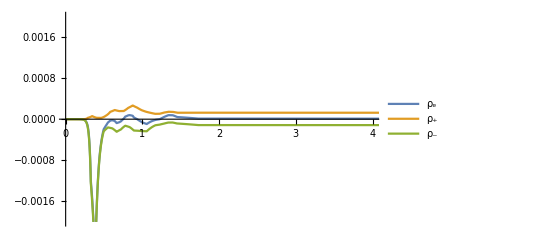

```mathematica
(*get the cation, anion, charge and solute density distribution in the EDL *)

CatRhoGRASolutions=Table[Interpolation[qcat  rho1M ConcFracValues[[i]] Exp[-( FGRAK[x] + qcat  (y[x]/.solutionsGra[[i]]))/kBTeV ],InterpolationOrder->0],{i,1,Length[solutionsGra]}];

AnionRhoGRASolutions=Table[Interpolation[qan   rho1M ConcFracValues[[i]] Exp[-(FGRAI[x] + qan  (y[x]/.solutionsGra[[i]]))/kBTeV ] ,InterpolationOrder->0],{i,1,Length[solutionsGra]}];

SoluteRhoGRASolutions=Table[Interpolation[Abs[qan   rho1M ConcFracValues[[i]] Exp[-(FGRAI[x] + qan  (y[x]/.solutionsGra[[i]]))/kBTeV ]] + Abs[qcat  rho1M ConcFracValues[[i]] Exp[-( FGRAK[x] + qcat  (y[x]/.solutionsGra[[i,1]]))/kBTeV ]],InterpolationOrder->0],{i,1,Length[solutionsGra]}];

RhoeGRASolutions=Table[Interpolation[qan   rho1M ConcFracValues[[i]] Exp[-(FGRAI[x] + qan  (y[x]/.solutionsGra[[i]]))/kBTeV ] + qcat  rho1M ConcFracValues[[i]] Exp[-( FGRAK[x] + qcat  (y[x]/.solutionsGra[[i]]))/kBTeV ],InterpolationOrder->0],{i,1,Length[solutionsGra]}];


Plot[{RhoeGRASolutions[[2]][x],CatRhoGRASolutions[[2]][x],AnionRhoGRASolutions[[2]][x]}
 ,{x,0,5},PlotRange->{{0,4},{-.002,.002}},PlotLegends->{"ρ_e","ρ_+","ρ_-"}]
```

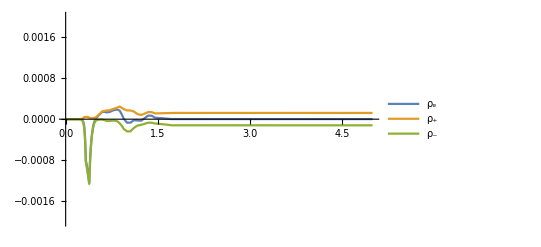

```mathematica
CatRhoBNSolutions=Table[Interpolation[qcat  rho1M ConcFracValues[[i]] Exp[-( FBNK[x] + qcat  (y[x]/.solutionsBN[[i]]))/kBTeV ],InterpolationOrder->0],{i,1,Length[solutionsBN]}];

AnionRhoBNSolutions=Table[Interpolation[qan   rho1M ConcFracValues[[i]] Exp[-(FBNI[x] + qan  (y[x]/.solutionsBN[[i]]))/kBTeV ] ,InterpolationOrder->0],{i,1,Length[solutionsBN]}];

RhoeBNSolutions=Table[Interpolation[qan   rho1M ConcFracValues[[i]] Exp[-(FBNI[x] + qan  (y[x]/.solutionsBN[[i]]))/kBTeV ] + qcat  rho1M ConcFracValues[[i]] Exp[-( FBNK[x] + qcat  (y[x]/.solutionsBN[[i]]))/kBTeV ],InterpolationOrder->0],{i,1,Length[solutionsGra]}];

SoluteRhoBNSolutions=Table[Interpolation[Abs[qan   rho1M ConcFracValues[[i]] Exp[-(FBNI[x] + qan  (y[x]/.solutionsBN[[i]]))/kBTeV ]] + Abs[qcat  rho1M ConcFracValues[[i]] Exp[-( FBNK[x] + qcat  (y[x]/.solutionsBN[[i]]))/kBTeV ]],InterpolationOrder->0],{i,1,Length[solutionsGra]}];

Plot[{RhoeBNSolutions[[2]][x],CatRhoBNSolutions[[2]][x],AnionRhoBNSolutions[[2]][x]}
 ,{x,0,5},PlotRange->{{0,5},{-.002,.002}},PlotLegends->{"ρ_e","ρ_+","ρ_-"}]
```

```mathematica
FilmHeight=Table[x,{x,0,xinf,0.01}];
AnRhoGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@AnionRhoGRASolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

RhoeGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@RhoeGRASolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

SoluteGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@SoluteRhoGRASolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

CatRhoGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@CatRhoGRASolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

AnRhoBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@AnionRhoBNSolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

RhoeBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@RhoeBNSolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

SoluteBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@SoluteRhoBNSolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

CatRhoBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@CatRhoBNSolutions[[i]][x],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];
```

```mathematica
Export[EXPDIR<>"/RhoGraConcAn.dat",AnRhoGraMat];
Export[EXPDIR<>"/RhoGraConcCat.dat",CatRhoGraMat];
Export[EXPDIR<>"/RhoeGraConc.dat",RhoeGraMat];
Export[EXPDIR<>"/SoluteProfileGraConc.dat",SoluteGraMat];

Export[EXPDIR<>"/RhoBNConcAn.dat",AnRhoBNMat];
Export[EXPDIR<>"/RhoBNConcCat.dat",CatRhoBNMat];
Export[EXPDIR<>"/RhoeBNConc.dat",RhoeBNMat];
Export[EXPDIR<>"/SoluteProfileBNConc.dat",SoluteBNMat];
```

```mathematica
Clear[WaterDensityContrib]
WaterDensityContrib[dens_,x_,rhofrac_,bulkdens_]:=rho1M rhofrac/bulkdens*Interpolation[  dens,InterpolationOrder->1][x];

WatGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@WaterDensityContrib[MeanRhoWatGraLim,x,ConcFracValues[[i]],BulkWatDens],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];


PsiGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@((y[x])/.solutionsGra[[i,1]]),{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

PsiBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@((y[x])/.solutionsBN[[i,1]]),{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

WatBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@WaterDensityContrib[MeanRhoWatBNLim,x,ConcFracValues[[i]],BulkWatDens],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

SoluteWatGraMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@SoluteRhoGRASolutions[[i]][x]- 2*Evaluate@WaterDensityContrib[MeanRhoWatGraLim,x,ConcFracValues[[i]],BulkWatDens],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];

SoluteWatBNMat=Transpose[Prepend[Table[Evaluate@Table[Evaluate@SoluteRhoBNSolutions[[i]][x]- 2*Evaluate@WaterDensityContrib[MeanRhoWatBNLim,x,ConcFracValues[[i]],BulkWatDens],{x,0,xinf,0.01}],{i,1,Length[ConcFracValues]}],FilmHeight]];
```

```mathematica
Export[EXPDIR<>"/IntegratedWatDensGra.dat",WatGraMat];
Export[EXPDIR<>"/IntegratedWatDensBN.dat",WatBNMat];
Export[EXPDIR<>"/SoluteWatProfileGraConc.dat",SoluteWatGraMat];
Export[EXPDIR<>"/SoluteWatProfileBNConc.dat",SoluteWatBNMat];
Export[EXPDIR<>"/PoissonPotGRAConc.dat",PsiGraMat];
Export[EXPDIR<>"/PoissonPotBNConc.dat",PsiBNMat];
```

```mathematica
ZetaGraSlip= Table[-(1.0/eps )NIntegrate[RhoeGRASolutions[[i]][x] (x+  bGra),{x,0,xinf}],{i,1,Length[ConcFracValues]}];
ZetaBNSlip= Table[-(1.0/eps )NIntegrate[RhoeBNSolutions[[i]][x] (x+ bBN),{x,0,xinf}],{i,1,Length[ConcFracValues]}];
```

```mathematica
Mdo1Gra=Table[NIntegrate[(SoluteRhoGRASolutions[[i]][x]  - 2 *WaterDensityContrib[MeanRhoWatGraLim,x,ConcFracValues[[i]],BulkWatDens]) (x+  bGra),{x,0,xinf}],{i,1,Length[ConcFracValues]}];


Mdo1BN=Table[NIntegrate[(SoluteRhoBNSolutions[[i]][x]  -2 * WaterDensityContrib[MeanRhoWatBNLim,x,ConcFracValues[[i]],BulkWatDens] ) (x+  bBN),{x,0,xinf}],{i,1,Length[ConcFracValues]}];
```

```mathematica
Mdo2TableGra=Table[NIntegrate[    (   SoluteRhoGRASolutions[[i]][x] - 2* WaterDensityContrib[MeanRhoWatGraLim,x,ConcFracValues[[i]], BulkWatDens  ]) 
(((y[x]-y[0])/.solutionsGra[[i,1]])/kBTeV/(4Pi lB))
,{x,0,xinf}
 ,Method->{Automatic,"SymbolicProcessing"->0},PrecisionGoal->6
],{i,1,Length[ConcFracValues]}];
```

```mathematica
Mdo2TableBN=Table[NIntegrate[    (   SoluteRhoBNSolutions[[i]][x] - 2* WaterDensityContrib[MeanRhoWatBNLim,x,ConcFracValues[[i]], BulkWatDens  ]) 
(((y[x]-y[0])/.solutionsBN[[i,1]])/kBTeV/(4Pi lB))
,{x,0,xinf}
 ,Method->{Automatic,"SymbolicProcessing"->0},PrecisionGoal->6
],{i,1,Length[ConcFracValues]}];
```

```mathematica
heading="#conc [M], zeta [V], Mdo1, Med2";
Export[EXPDIR<>"/Transport_Coeffs_Gra.dat",
Prepend[
Table[ {ConcFracValues[[i]],ZetaGraSlip[[i]],Mdo1Gra[[i]] ,Mdo2TableGra[[i]]},{i,1,Length[ConcFracValues] }]  ,heading]];

heading="#conc [M], zeta [V], Mdo1, Med2
";
Export[EXPDIR<>"/Transport_Coeffs_BN.dat",
Prepend[
Table[ {ConcFracValues[[i]],ZetaBNSlip[[i]],Mdo1BN[[i]] ,Mdo2TableBN[[i]]
},{i,1,Length[ConcFracValues] }]  ,heading]];
```